```mathematica
0.03/(24*60)
```

0.0000208333

```mathematica
β=0.1;
γ=0.03;
t1 = 0;
t2 =100;
cmat = {
{1,1,0},
{1,1,1},
{0,1,1}
};
n = {3000, 3000, 3000};
s[t_]:={s1[t] ,s2[t] ,s3[t] };
i[t_]:={i1[t] ,i2[t] ,i3[t] };
r[t_]:={r1[t] ,r2[t] ,r3[t] };
λ[a_,t_]:= β  Sum[ cmat[[a,b]] (i[t][[b]])/n[[b]],{b,1,3}]
```

```mathematica
sol = NDSolve[{
s'[t][[1]]== -λ[1,t] s[t][[1]],
s'[t][[2]]== -λ[2,t] s[t][[2]],
s'[t][[3]]== -λ[3,t] s[t][[3]],
i'[t][[1]]== λ[1,t] s[t][[1]] -γ i[t][[1]],
i'[t][[2]]== λ[2,t] s[t][[2]] -γ i[t][[2]],
i'[t][[3]]== λ[3,t] s[t][[3]] -γ i[t][[3]],
r'[t][[1]]== γ i[t][[1]],
r'[t][[2]]== γ i[t][[2]],
r'[t][[3]]== γ i[t][[3]],
s[0][[1]]== n[[1]],
s[0][[2]]== n[[2]],
s[0][[3]]== n[[3]],
i[0][[1]]==1,
i[0][[2]]== 0,
i[0][[3]]==0,
r[0][[1]]== 0,
r[0][[2]]== 0,
r[0][[3]]==0
},Join[s[t],r[t],i[t]],{t,t1,t2}]
```

{{s1[t]→InterpolatingFunction[…][t],s2[t]→InterpolatingFunction[…][t],s3[t]→InterpolatingFunction[…][t],r1[t]→InterpolatingFunction[…][t],r2[t]→InterpolatingFunction[…][t],r3[t]→InterpolatingFunction[…][t],i1[t]→InterpolatingFunction[…][t],i2[t]→InterpolatingFunction[…][t],i3[t]→InterpolatingFunction[…][t]}}

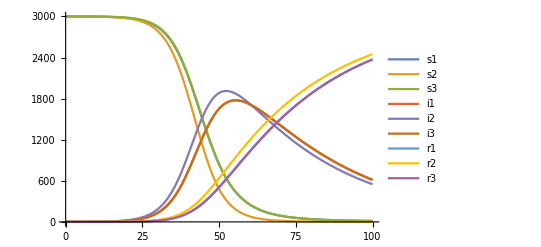

```mathematica
sols = Join[s[t],i[t],r[t]]/.sol//Flatten;
Plot[sols, {t,t1,t2},
PlotLegends->{"s1", "s2", "s3", "i1", "i2", "i3", "r1", "r2", "r3"}]
```

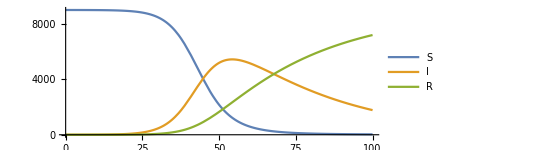

```mathematica
Plot[{
Total[s[t]/.sol//Flatten],
Total[i[t]/.sol//Flatten],
Total[r[t]/.sol//Flatten]
},{t,t1,t2},PlotLegends-> {"S","I","R"},AspectRatio->3/8]
```

```mathematica
x=Table[sols[[1]],{t,t1,t2,1/60}]
```

{3000.,3000.,3000.,2999.99,2999.99,2999.99,2999.99,2999.99,2999.99,2999.98,2999.98,2999.98,2999.98,2999.98,2999.98,2999.97,2999.97,2999.97,2999.97,2999.97,2999.97,2999.96,2999.96,2999.96,2999.96,2999.96,2999.96,2999.95,2999.95,2999.95,2999.95,2999.95,2999.94,2999.94,2999.94,2999.94,2999.94,2999.93,2999.93,2999.93,2999.93,2999.93,2999.93,2999.92,2999.92,2999.92,2999.92,2999.92,2999.91,2999.91,2999.91,2999.91,2999.91,2999.9,2999.9,2999.9,2999.9,2999.9,2999.89,2999.89,2999.89,2999.89,2999.89,2999.89,2999.88,2999.88,2999.88,2999.88,2999.88,2999.87,2999.87,2999.87,2999.87,2999.86,2999.86,2999.86,2999.86,2999.86,2999.85,2999.85,2999.85,2999.85,2999.85,2999.84,2999.84,2999.84,2999.84,2999.84,2999.83,2999.83,2999.83,2999.83,2999.82,2999.82,2999.82,2999.82,2999.82,2999.81,2999.81,2999.81,2999.81,2999.81,2999.8,2999.8,2999.8,2999.8,2999.79,2999.79,2999.79,2999.79,2999.78,2999.78,2999.78,2999.78,2999.78,2999.77,2999.77,2999.77,2999.77,2999.76,2999.76,2999.76,2999.76,2999.75,2999.75,2999.75,2999.75,2999.75,2999.74,2999.74,2999.74,2999.74,2999.73,2999.73,2999.73,2999.73,2999.72,2999.72,2999.72,2999.72,2999.71,2999.71,2999.71,2999.71,2999.7,2999.7,2999.7,2999.7,2999.69,2999.69,2999.69,2999.69,2999.68,2999.68,2999.68,2999.68,2999.67,2999.67,2999.67,2999.67,2999.66,2999.66,2999.66,2999.65,2999.65,2999.65,2999.65,2999.64,2999.64,2999.64,2999.64,2999.63,2999.63,2999.63,2999.62,2999.62,2999.62,2999.62,2999.61,2999.61,2999.61,2999.61,2999.6,2999.6,2999.6,2999.59,2999.59,2999.59,2999.59,2999.58,2999.58,2999.58,2999.57,2999.57,2999.57,2999.57,2999.56,2999.56,2999.56,2999.55,2999.55,2999.55,2999.54,2999.54,2999.54,2999.54,2999.53,2999.53,2999.53,2999.52,2999.52,2999.52,2999.51,2999.51,2999.51,2999.51,2999.5,2999.5,2999.5,2999.49,2999.49,2999.49,2999.48,2999.48,2999.48,2999.47,2999.47,2999.47,2999.46,2999.46,2999.46,2999.46,2999.45,2999.45,2999.45,2999.44,2999.44,2999.44,2999.43,2999.43,2999.43,2999.42,2999.42,2999.42,2999.41,2999.41,2999.41,2999.4,2999.4,2999.4,2999.39,2999.39,2999.39,2999.38,2999.38,2999.37,2999.37,2999.37,2999.36,2999.36,2999.36,2999.35,2999.35,2999.35,2999.34,2999.34,2999.34,2999.33,2999.33,2999.33,2999.32,2999.32,2999.31,2999.31,2999.31,2999.3,2999.3,2999.3,2999.29,2999.29,2999.29,2999.28,2999.28,2999.27,2999.27,2999.27,2999.26,2999.26,2999.25,2999.25,2999.25,2999.24,2999.24,2999.24,2999.23,2999.23,2999.22,2999.22,2999.22,2999.21,2999.21,2999.2,2999.2,2999.2,2999.19,2999.19,2999.18,2999.18,2999.18,2999.17,2999.17,2999.16,2999.16,2999.16,2999.15,2999.15,2999.14,2999.14,2999.14,2999.13,2999.13,2999.12,2999.12,2999.11,2999.11,2999.11,2999.1,2999.1,2999.09,2999.09,2999.08,2999.08,2999.08,2999.07,2999.07,2999.06,2999.06,2999.05,2999.05,2999.04,2999.04,2999.04,2999.03,2999.03,2999.02,2999.02,2999.01,2999.01,2999.,2999.,2998.99,2998.99,2998.99,2998.98,2998.98,2998.97,2998.97,2998.96,2998.96,2998.95,2998.95,2998.94,2998.94,2998.93,2998.93,2998.92,2998.92,2998.91,2998.91,2998.91,2998.9,2998.9,2998.89,2998.89,2998.88,2998.88,2998.87,2998.87,2998.86,2998.86,2998.85,2998.85,2998.84,2998.84,2998.83,2998.83,2998.82,2998.82,2998.81,2998.81,2998.8,2998.79,2998.79,2998.78,2998.78,2998.77,2998.77,2998.76,2998.76,2998.75,2998.75,2998.74,2998.74,2998.73,2998.73,2998.72,2998.72,2998.71,2998.7,2998.7,2998.69,2998.69,2998.68,2998.68,2998.67,2998.67,2998.66,2998.65,2998.65,2998.64,2998.64,2998.63,2998.63,2998.62,2998.61,2998.61,2998.6,2998.6,2998.59,2998.59,2998.58,2998.57,2998.57,2998.56,2998.56,2998.55,2998.54,2998.54,2998.53,2998.53,2998.52,2998.51,2998.51,2998.5,2998.5,2998.49,2998.48,2998.48,2998.47,2998.47,2998.46,2998.45,2998.45,2998.44,2998.43,2998.43,2998.42,2998.42,2998.41,2998.4,2998.4,2998.39,2998.38,2998.38,2998.37,2998.36,2998.36,2998.35,2998.34,2998.34,2998.33,2998.32,2998.32,2998.31,2998.3,2998.3,2998.29,2998.28,2998.28,2998.27,2998.26,2998.26,2998.25,2998.24,2998.24,2998.23,2998.22,2998.22,2998.21,2998.2,2998.19,2998.19,2998.18,2998.17,2998.17,2998.16,2998.15,2998.14,2998.14,2998.13,2998.12,2998.12,2998.11,2998.1,2998.09,2998.09,2998.08,2998.07,2998.06,2998.06,2998.05,2998.04,2998.03,2998.03,2998.02,2998.01,2998.,2998.,2997.99,2997.98,2997.97,2997.97,2997.96,2997.95,2997.94,2997.93,2997.93,2997.92,2997.91,2997.9,2997.9,2997.89,2997.88,2997.87,2997.86,2997.86,2997.85,2997.84,2997.83,2997.82,2997.81,2997.81,2997.8,2997.79,2997.78,2997.77,2997.76,2997.76,2997.75,2997.74,2997.73,2997.72,2997.71,2997.71,2997.7,2997.69,2997.68,2997.67,2997.66,2997.65,2997.65,2997.64,2997.63,2997.62,2997.61,2997.6,2997.59,2997.58,2997.57,2997.57,2997.56,2997.55,2997.54,2997.53,2997.52,2997.51,2997.5,2997.49,2997.48,2997.47,2997.46,2997.46,2997.45,2997.44,2997.43,2997.42,2997.41,2997.4,2997.39,2997.38,2997.37,2997.36,2997.35,2997.34,2997.33,2997.32,2997.31,2997.3,2997.29,2997.28,2997.27,2997.26,2997.25,2997.24,2997.23,2997.22,2997.21,2997.2,2997.19,2997.18,2997.17,2997.16,2997.15,2997.14,2997.13,2997.12,2997.11,2997.1,2997.09,2997.08,2997.07,2997.06,2997.05,2997.04,2997.03,2997.02,2997.,2996.99,2996.98,2996.97,2996.96,2996.95,2996.94,2996.93,2996.92,2996.91,2996.89,2996.88,2996.87,2996.86,2996.85,2996.84,2996.83,2996.82,2996.8,2996.79,2996.78,2996.77,2996.76,2996.75,2996.74,2996.72,2996.71,2996.7,2996.69,2996.68,2996.67,2996.65,2996.64,2996.63,2996.62,2996.61,2996.59,2996.58,2996.57,2996.56,2996.55,2996.53,2996.52,2996.51,2996.5,2996.48,2996.47,2996.46,2996.45,2996.43,2996.42,2996.41,2996.4,2996.38,2996.37,2996.36,2996.34,2996.33,2996.32,2996.31,2996.29,2996.28,2996.27,2996.25,2996.24,2996.23,2996.21,2996.2,2996.19,2996.17,2996.16,2996.15,2996.13,2996.12,2996.11,2996.09,2996.08,2996.07,2996.05,2996.04,2996.02,2996.01,2996.,2995.98,2995.97,2995.95,2995.94,2995.93,2995.91,2995.9,2995.88,2995.87,2995.85,2995.84,2995.82,2995.81,2995.8,2995.78,2995.77,2995.75,2995.74,2995.72,2995.71,2995.69,2995.68,2995.66,2995.65,2995.63,2995.62,2995.6,2995.59,2995.57,2995.56,2995.54,2995.52,2995.51,2995.49,2995.48,2995.46,2995.45,2995.43,2995.41,2995.4,2995.38,2995.37,2995.35,2995.33,2995.32,2995.3,2995.29,2995.27,2995.25,2995.24,2995.22,2995.2,2995.19,2995.17,2995.15,2995.14,2995.12,2995.1,2995.09,2995.07,2995.05,2995.04,2995.02,2995.,2994.98,2994.97,2994.95,2994.93,2994.91,2994.9,2994.88,2994.86,2994.84,2994.83,2994.81,2994.79,2994.77,2994.76,2994.74,2994.72,2994.7,2994.68,2994.66,2994.65,2994.63,2994.61,2994.59,2994.57,2994.55,2994.53,2994.52,2994.5,2994.48,2994.46,2994.44,2994.42,2994.4,2994.38,2994.36,2994.34,2994.33,2994.31,2994.29,2994.27,2994.25,2994.23,2994.21,2994.19,2994.17,2994.15,2994.13,2994.11,2994.09,2994.07,2994.05,2994.03,2994.01,2993.99,2993.97,2993.94,2993.92,2993.9,2993.88,2993.86,2993.84,2993.82,2993.8,2993.78,2993.76,2993.73,2993.71,2993.69,2993.67,2993.65,2993.63,2993.61,2993.58,2993.56,2993.54,2993.52,2993.5,2993.47,2993.45,2993.43,2993.41,2993.38,2993.36,2993.34,2993.32,2993.29,2993.27,2993.25,2993.23,2993.2,2993.18,2993.16,2993.13,2993.11,2993.09,2993.06,2993.04,2993.02,2992.99,2992.97,2992.94,2992.92,2992.9,2992.87,2992.85,2992.82,2992.8,2992.77,2992.75,2992.72,2992.7,2992.68,2992.65,2992.63,2992.6,2992.58,2992.55,2992.53,2992.5,2992.47,2992.45,2992.42,2992.4,2992.37,2992.35,2992.32,2992.29,2992.27,2992.24,2992.22,2992.19,2992.16,2992.14,2992.11,2992.08,2992.06,2992.03,2992.,2991.97,2991.95,2991.92,2991.89,2991.87,2991.84,2991.81,2991.78,2991.75,2991.73,2991.7,2991.67,2991.64,2991.61,2991.59,2991.56,2991.53,2991.5,2991.47,2991.44,2991.41,2991.38,2991.36,2991.33,2991.3,2991.27,2991.24,2991.21,2991.18,2991.15,2991.12,2991.09,2991.06,2991.03,2991.,2990.97,2990.94,2990.91,2990.88,2990.85,2990.81,2990.78,2990.75,2990.72,2990.69,2990.66,2990.63,2990.59,2990.56,2990.53,2990.5,2990.47,2990.44,2990.4,2990.37,2990.34,2990.31,2990.27,2990.24,2990.21,2990.17,2990.14,2990.11,2990.07,2990.04,2990.01,2989.97,2989.94,2989.91,2989.87,2989.84,2989.8,2989.77,2989.73,2989.7,2989.66,2989.63,2989.59,2989.56,2989.52,2989.49,2989.45,2989.42,2989.38,2989.35,2989.31,2989.27,2989.24,2989.2,2989.17,2989.13,2989.09,2989.06,2989.02,2988.98,2988.95,2988.91,2988.87,2988.83,2988.8,2988.76,2988.72,2988.68,2988.64,2988.61,2988.57,2988.53,2988.49,2988.45,2988.41,2988.37,2988.33,2988.29,2988.26,2988.22,2988.18,2988.14,2988.1,2988.06,2988.02,2987.98,2987.93,2987.89,2987.85,2987.81,2987.77,2987.73,2987.69,2987.65,2987.61,2987.56,2987.52,2987.48,2987.44,2987.4,2987.35,2987.31,2987.27,2987.23,2987.18,2987.14,2987.1,2987.05,2987.01,2986.97,2986.92,2986.88,2986.83,2986.79,2986.74,2986.7,2986.66,2986.61,2986.57,2986.52,2986.47,2986.43,2986.38,2986.34,2986.29,2986.25,2986.2,2986.15,2986.11,2986.06,2986.01,2985.97,2985.92,2985.87,2985.82,2985.78,2985.73,2985.68,2985.63,2985.58,2985.53,2985.49,2985.44,2985.39,2985.34,2985.29,2985.24,2985.19,2985.14,2985.09,2985.04,2984.99,2984.94,2984.89,2984.84,2984.79,2984.74,2984.68,2984.63,2984.58,2984.53,2984.48,2984.43,2984.37,2984.32,2984.27,2984.21,2984.16,2984.11,2984.05,2984.,2983.95,2983.89,2983.84,2983.78,2983.73,2983.68,2983.62,2983.57,2983.51,2983.45,2983.4,2983.34,2983.29,2983.23,2983.17,2983.12,2983.06,2983.,2982.95,2982.89,2982.83,2982.77,2982.72,2982.66,2982.6,2982.54,2982.48,2982.42,2982.36,2982.31,2982.25,2982.19,2982.13,2982.07,2982.01,2981.95,2981.88,2981.82,2981.76,2981.7,2981.64,2981.58,2981.52,2981.45,2981.39,2981.33,2981.27,2981.2,2981.14,2981.08,2981.01,2980.95,2980.88,2980.82,2980.76,2980.69,2980.63,2980.56,2980.5,2980.43,2980.36,2980.3,2980.23,2980.17,2980.1,2980.03,2979.96,2979.9,2979.83,2979.76,2979.69,2979.63,2979.56,2979.49,2979.42,2979.35,2979.28,2979.21,2979.14,2979.07,2979.,2978.93,2978.86,2978.79,2978.72,2978.64,2978.57,2978.5,2978.43,2978.36,2978.28,2978.21,2978.14,2978.06,2977.99,2977.92,2977.84,2977.77,2977.69,2977.62,2977.54,2977.47,2977.39,2977.31,2977.24,2977.16,2977.08,2977.01,2976.93,2976.85,2976.77,2976.7,2976.62,2976.54,2976.46,2976.38,2976.3,2976.22,2976.14,2976.06,2975.98,2975.9,2975.82,2975.74,2975.66,2975.57,2975.49,2975.41,2975.33,2975.24,2975.16,2975.08,2974.99,2974.91,2974.82,2974.74,2974.66,2974.57,2974.48,2974.4,2974.31,2974.23,2974.14,2974.05,2973.97,2973.88,2973.79,2973.7,2973.61,2973.52,2973.44,2973.35,2973.26,2973.17,2973.08,2972.99,2972.89,2972.8,2972.71,2972.62,2972.53,2972.44,2972.34,2972.25,2972.16,2972.06,2971.97,2971.87,2971.78,2971.68,2971.59,2971.49,2971.4,2971.3,2971.21,2971.11,2971.01,2970.91,2970.82,2970.72,2970.62,2970.52,2970.42,2970.32,2970.22,2970.12,2970.02,2969.92,2969.82,2969.72,2969.62,2969.51,2969.41,2969.31,2969.2,2969.1,2969.,2968.89,2968.79,2968.68,2968.58,2968.47,2968.37,2968.26,2968.15,2968.05,2967.94,2967.83,2967.72,2967.61,2967.5,2967.39,2967.28,2967.17,2967.06,2966.95,2966.84,2966.73,2966.62,2966.51,2966.39,2966.28,2966.17,2966.05,2965.94,2965.82,2965.71,2965.59,2965.48,2965.36,2965.25,2965.13,2965.01,2964.89,2964.78,2964.66,2964.54,2964.42,2964.3,2964.18,2964.06,2963.94,2963.82,2963.7,2963.57,2963.45,2963.33,2963.2,2963.08,2962.96,2962.83,2962.71,2962.58,2962.46,2962.33,2962.2,2962.08,2961.95,2961.82,2961.69,2961.56,2961.43,2961.3,2961.17,2961.04,2960.91,2960.78,2960.65,2960.52,2960.38,2960.25,2960.12,2959.98,2959.85,2959.71,2959.58,2959.44,2959.3,2959.17,2959.03,2958.89,2958.75,2958.62,2958.48,2958.34,2958.2,2958.06,2957.92,2957.77,2957.63,2957.49,2957.35,2957.2,2957.06,2956.91,2956.77,2956.62,2956.48,2956.33,2956.19,2956.04,2955.89,2955.74,2955.59,2955.44,2955.29,2955.14,2954.99,2954.84,2954.69,2954.54,2954.39,2954.23,2954.08,2953.92,2953.77,2953.61,2953.46,2953.3,2953.14,2952.99,2952.83,2952.67,2952.51,2952.35,2952.19,2952.03,2951.87,2951.71,2951.55,2951.38,2951.22,2951.06,2950.89,2950.73,2950.56,2950.39,2950.23,2950.06,2949.89,2949.72,2949.56,2949.39,2949.22,2949.05,2948.87,2948.7,2948.53,2948.36,2948.18,2948.01,2947.84,2947.66,2947.48,2947.31,2947.13,2946.95,2946.78,2946.6,2946.42,2946.24,2946.06,2945.88,2945.69,2945.51,2945.33,2945.15,2944.96,2944.78,2944.59,2944.41,2944.22,2944.03,2943.84,2943.66,2943.47,2943.28,2943.09,2942.9,2942.7,2942.51,2942.32,2942.13,2941.93,2941.74,2941.54,2941.35,2941.15,2940.95,2940.75,2940.55,2940.35,2940.15,2939.95,2939.75,2939.55,2939.35,2939.14,2938.94,2938.74,2938.53,2938.32,2938.12,2937.91,2937.7,2937.49,2937.28,2937.07,2936.86,2936.65,2936.44,2936.23,2936.01,2935.8,2935.58,2935.37,2935.15,2934.93,2934.72,2934.5,2934.28,2934.06,2933.84,2933.61,2933.39,2933.17,2932.95,2932.72,2932.5,2932.27,2932.04,2931.82,2931.59,2931.36,2931.13,2930.9,2930.67,2930.43,2930.2,2929.97,2929.73,2929.5,2929.26,2929.03,2928.79,2928.55,2928.31,2928.07,2927.83,2927.59,2927.35,2927.11,2926.86,2926.62,2926.37,2926.13,2925.88,2925.63,2925.38,2925.13,2924.88,2924.63,2924.38,2924.13,2923.87,2923.62,2923.36,2923.11,2922.85,2922.59,2922.33,2922.08,2921.81,2921.55,2921.29,2921.03,2920.77,2920.5,2920.24,2919.97,2919.7,2919.43,2919.17,2918.9,2918.62,2918.35,2918.08,2917.81,2917.53,2917.26,2916.98,2916.71,2916.43,2916.15,2915.87,2915.59,2915.31,2915.03,2914.74,2914.46,2914.17,2913.89,2913.6,2913.31,2913.02,2912.73,2912.44,2912.15,2911.86,2911.56,2911.27,2910.97,2910.68,2910.38,2910.08,2909.78,2909.48,2909.18,2908.88,2908.58,2908.27,2907.97,2907.66,2907.35,2907.05,2906.74,2906.43,2906.12,2905.8,2905.49,2905.18,2904.86,2904.54,2904.23,2903.91,2903.59,2903.27,2902.95,2902.63,2902.3,2901.98,2901.65,2901.33,2901.,2900.67,2900.34,2900.01,2899.68,2899.34,2899.01,2898.67,2898.34,2898.,2897.66,2897.32,2896.98,2896.64,2896.3,2895.95,2895.61,2895.26,2894.92,2894.57,2894.22,2893.87,2893.52,2893.16,2892.81,2892.46,2892.1,2891.74,2891.38,2891.02,2890.66,2890.3,2889.94,2889.57,2889.21,2888.84,2888.47,2888.11,2887.74,2887.36,2886.99,2886.62,2886.24,2885.87,2885.49,2885.11,2884.73,2884.35,2883.97,2883.59,2883.2,2882.82,2882.43,2882.04,2881.65,2881.26,2880.87,2880.48,2880.08,2879.69,2879.29,2878.89,2878.49,2878.09,2877.69,2877.29,2876.88,2876.48,2876.07,2875.66,2875.25,2874.84,2874.43,2874.02,2873.6,2873.19,2872.77,2872.35,2871.93,2871.51,2871.09,2870.66,2870.24,2869.81,2869.38,2868.95,2868.52,2868.09,2867.66,2867.22,2866.79,2866.35,2865.91,2865.47,2865.03,2864.59,2864.14,2863.7,2863.25,2862.8,2862.35,2861.9,2861.45,2860.99,2860.54,2860.08,2859.62,2859.16,2858.7,2858.24,2857.77,2857.31,2856.84,2856.37,2855.9,2855.43,2854.96,2854.49,2854.01,2853.53,2853.05,2852.57,2852.09,2851.61,2851.12,2850.64,2850.15,2849.66,2849.17,2848.68,2848.18,2847.69,2847.19,2846.69,2846.19,2845.69,2845.19,2844.69,2844.18,2843.67,2843.16,2842.65,2842.14,2841.63,2841.11,2840.59,2840.07,2839.55,2839.03,2838.51,2837.98,2837.46,2836.93,2836.4,2835.87,2835.33,2834.8,2834.26,2833.73,2833.19,2832.65,2832.1,2831.56,2831.01,2830.46,2829.91,2829.36,2828.81,2828.26,2827.7,2827.14,2826.58,2826.02,2825.46,2824.89,2824.33,2823.76,2823.19,2822.62,2822.04,2821.47,2820.89,2820.31,2819.73,2819.15,2818.57,2817.98,2817.39,2816.81,2816.21,2815.62,2815.03,2814.43,2813.83,2813.23,2812.63,2812.03,2811.42,2810.82,2810.21,2809.6,2808.99,2808.37,2807.76,2807.14,2806.52,2805.9,2805.27,2804.65,2804.02,2803.39,2802.76,2802.13,2801.49,2800.86,2800.22,2799.58,2798.94,2798.29,2797.65,2797.,2796.35,2795.7,2795.04,2794.39,2793.73,2793.07,2792.41,2791.75,2791.08,2790.41,2789.75,2789.07,2788.4,2787.73,2787.05,2786.37,2785.69,2785.01,2784.32,2783.63,2782.95,2782.26,2781.56,2780.87,2780.17,2779.47,2778.77,2778.07,2777.36,2776.65,2775.95,2775.23,2774.52,2773.81,2773.09,2772.37,2771.65,2770.92,2770.2,2769.47,2768.74,2768.01,2767.27,2766.54,2765.8,2765.06,2764.32,2763.57,2762.82,2762.08,2761.32,2760.57,2759.82,2759.06,2758.3,2757.54,2756.77,2756.01,2755.24,2754.47,2753.69,2752.92,2752.14,2751.36,2750.58,2749.8,2749.01,2748.22,2747.43,2746.64,2745.85,2745.05,2744.25,2743.45,2742.64,2741.84,2741.03,2740.22,2739.41,2738.59,2737.77,2736.95,2736.13,2735.31,2734.48,2733.65,2732.82,2731.99,2731.15,2730.31,2729.47,2728.63,2727.78,2726.94,2726.09,2725.24,2724.38,2723.52,2722.66,2721.8,2720.94,2720.07,2719.2,2718.33,2717.46,2716.58,2715.7,2714.82,2713.94,2713.06,2712.17,2711.28,2710.38,2709.49,2708.59,2707.69,2706.79,2705.88,2704.98,2704.07,2703.15,2702.24,2701.32,2700.4,2699.48,2698.56,2697.63,2696.7,2695.77,2694.83,2693.9,2692.96,2692.01,2691.07,2690.12,2689.17,2688.22,2687.27,2686.31,2685.35,2684.39,2683.42,2682.45,2681.48,2680.51,2679.54,2678.56,2677.58,2676.59,2675.61,2674.62,2673.63,2672.64,2671.64,2670.64,2669.64,2668.64,2667.63,2666.62,2665.61,2664.6,2663.58,2662.56,2661.54,2660.51,2659.49,2658.46,2657.42,2656.39,2655.35,2654.31,2653.27,2652.22,2651.17,2650.12,2649.07,2648.01,2646.95,2645.89,2644.82,2643.76,2642.69,2641.61,2640.54,2639.46,2638.38,2637.29,2636.21,2635.12,2634.02,2632.93,2631.83,2630.73,2629.63,2628.52,2627.41,2626.3,2625.19,2624.07,2622.95,2621.83,2620.7,2619.58,2618.44,2617.31,2616.17,2615.04,2613.89,2612.75,2611.6,2610.45,2609.3,2608.14,2606.98,2605.82,2604.65,2603.49,2602.32,2601.14,2599.97,2598.79,2597.61,2596.42,2595.23,2594.04,2592.85,2591.65,2590.46,2589.25,2588.05,2586.84,2585.63,2584.42,2583.2,2581.98,2580.76,2579.54,2578.31,2577.08,2575.84,2574.61,2573.37,2572.12,2570.88,2569.63,2568.38,2567.13,2565.87,2564.61,2563.35,2562.08,2560.81,2559.54,2558.27,2556.99,2555.71,2554.42,2553.14,2551.85,2550.56,2549.26,2547.96,2546.66,2545.36,2544.05,2542.74,2541.43,2540.11,2538.79,2537.47,2536.14,2534.82,2533.48,2532.15,2530.81,2529.47,2528.13,2526.78,2525.43,2524.08,2522.73,2521.37,2520.01,2518.64,2517.28,2515.91,2514.53,2513.16,2511.78,2510.4,2509.01,2507.62,2506.23,2504.84,2503.44,2502.04,2500.64,2499.23,2497.82,2496.41,2494.99,2493.58,2492.15,2490.73,2489.3,2487.87,2486.44,2485.,2483.56,2482.12,2480.67,2479.22,2477.77,2476.32,2474.86,2473.4,2471.93,2470.47,2469.,2467.52,2466.05,2464.57,2463.08,2461.6,2460.11,2458.62,2457.12,2455.63,2454.13,2452.62,2451.11,2449.6,2448.09,2446.58,2445.06,2443.53,2442.01,2440.48,2438.95,2437.42,2435.88,2434.34,2432.79,2431.25,2429.7,2428.14,2426.59,2425.03,2423.47,2421.9,2420.33,2418.76,2417.19,2415.61,2414.03,2412.45,2410.86,2409.27,2407.68,2406.08,2404.49,2402.88,2401.28,2399.67,2398.06,2396.45,2394.83,2393.21,2391.59,2389.96,2388.33,2386.7,2385.07,2383.43,2381.79,2380.14,2378.5,2376.85,2375.19,2373.54,2371.88,2370.21,2368.55,2366.88,2365.21,2363.53,2361.86,2360.18,2358.49,2356.81,2355.12,2353.43,2351.73,2350.03,2348.33,2346.63,2344.92,2343.21,2341.49,2339.78,2338.06,2336.34,2334.61,2332.88,2331.15,2329.42,2327.68,2325.94,2324.2,2322.45,2320.7,2318.95,2317.19,2315.44,2313.68,2311.91,2310.14,2308.38,2306.6,2304.83,2303.05,2301.27,2299.48,2297.7,2295.91,2294.11,2292.32,2290.52,2288.72,2286.91,2285.1,2283.29,2281.48,2279.66,2277.85,2276.02,2274.2,2272.37,2270.54,2268.71,2266.87,2265.03,2263.19,2261.35,2259.5,2257.65,2255.8,2253.94,2252.08,2250.22,2248.35,2246.49,2244.62,2242.74,2240.87,2238.99,2237.11,2235.23,2233.34,2231.45,2229.56,2227.66,2225.76,2223.86,2221.96,2220.05,2218.15,2216.24,2214.32,2212.4,2210.48,2208.56,2206.64,2204.71,2202.78,2200.85,2198.91,2196.97,2195.03,2193.09,2191.14,2189.19,2187.24,2185.29,2183.33,2181.37,2179.41,2177.45,2175.48,2173.51,2171.54,2169.56,2167.59,2165.61,2163.62,2161.64,2159.65,2157.66,2155.67,2153.67,2151.67,2149.67,2147.67,2145.67,2143.66,2141.65,2139.64,2137.62,2135.6,2133.58,2131.56,2129.54,2127.51,2125.48,2123.45,2121.41,2119.38,2117.34,2115.29,2113.25,2111.2,2109.16,2107.1,2105.05,2102.99,2100.94,2098.88,2096.81,2094.75,2092.68,2090.61,2088.54,2086.46,2084.39,2082.31,2080.23,2078.15,2076.06,2073.97,2071.88,2069.79,2067.7,2065.6,2063.5,2061.4,2059.3,2057.19,2055.08,2052.98,2050.86,2048.75,2046.63,2044.52,2042.4,2040.27,2038.15,2036.02,2033.9,2031.77,2029.63,2027.5,2025.36,2023.22,2021.08,2018.94,2016.8,2014.65,2012.5,2010.35,2008.2,2006.05,2003.89,2001.73,1999.57,1997.41,1995.25,1993.08,1990.92,1988.75,1986.58,1984.4,1982.23,1980.05,1977.87,1975.69,1973.51,1971.33,1969.14,1966.96,1964.77,1962.58,1960.38,1958.19,1956.,1953.8,1951.6,1949.4,1947.2,1944.99,1942.79,1940.58,1938.37,1936.16,1933.95,1931.74,1929.52,1927.3,1925.09,1922.87,1920.64,1918.42,1916.2,1913.97,1911.74,1909.52,1907.29,1905.05,1902.82,1900.59,1898.35,1896.11,1893.87,1891.63,1889.39,1887.15,1884.91,1882.66,1880.41,1878.17,1875.92,1873.67,1871.41,1869.16,1866.91,1864.65,1862.39,1860.13,1857.88,1855.62,1853.35,1851.09,1848.83,1846.56,1844.29,1842.03,1839.76,1837.49,1835.22,1832.95,1830.67,1828.4,1826.12,1823.85,1821.57,1819.29,1817.01,1814.73,1812.45,1810.17,1807.89,1805.6,1803.32,1801.03,1798.75,1796.46,1794.17,1791.88,1789.59,1787.3,1785.01,1782.72,1780.42,1778.13,1775.84,1773.54,1771.24,1768.95,1766.65,1764.35,1762.05,1759.75,1757.45,1755.15,1752.85,1750.54,1748.24,1745.94,1743.63,1741.33,1739.02,1736.72,1734.41,1732.1,1729.79,1727.49,1725.18,1722.87,1720.56,1718.25,1715.94,1713.63,1711.31,1709.,1706.69,1704.38,1702.06,1699.75,1697.44,1695.12,1692.81,1690.49,1688.18,1685.86,1683.55,1681.23,1678.91,1676.6,1674.28,1671.96,1669.65,1667.33,1665.01,1662.69,1660.38,1658.06,1655.74,1653.42,1651.1,1648.78,1646.47,1644.15,1641.83,1639.51,1637.19,1634.87,1632.55,1630.23,1627.92,1625.6,1623.28,1620.96,1618.64,1616.32,1614.,1611.69,1609.37,1607.05,1604.73,1602.41,1600.1,1597.78,1595.46,1593.14,1590.83,1588.51,1586.19,1583.88,1581.56,1579.25,1576.93,1574.62,1572.3,1569.99,1567.67,1565.36,1563.05,1560.73,1558.42,1556.11,1553.8,1551.48,1549.17,1546.86,1544.55,1542.24,1539.93,1537.63,1535.32,1533.01,1530.7,1528.4,1526.09,1523.79,1521.48,1519.18,1516.87,1514.57,1512.27,1509.97,1507.66,1505.36,1503.06,1500.76,1498.47,1496.17,1493.87,1491.58,1489.28,1486.98,1484.69,1482.4,1480.1,1477.81,1475.52,1473.23,1470.94,1468.65,1466.37,1464.08,1461.79,1459.51,1457.22,1454.94,1452.66,1450.38,1448.1,1445.82,1443.54,1441.26,1438.98,1436.71,1434.43,1432.16,1429.89,1427.62,1425.35,1423.08,1420.81,1418.54,1416.28,1414.01,1411.75,1409.48,1407.22,1404.96,1402.7,1400.44,1398.19,1395.93,1393.68,1391.42,1389.17,1386.92,1384.67,1382.42,1380.17,1377.93,1375.68,1373.44,1371.2,1368.96,1366.72,1364.48,1362.24,1360.,1357.77,1355.54,1353.31,1351.08,1348.85,1346.62,1344.39,1342.17,1339.95,1337.72,1335.5,1333.29,1331.07,1328.85,1326.64,1324.43,1322.22,1320.01,1317.8,1315.59,1313.39,1311.18,1308.98,1306.78,1304.58,1302.38,1300.19,1297.99,1295.8,1293.61,1291.42,1289.23,1287.05,1284.86,1282.68,1280.5,1278.32,1276.14,1273.97,1271.79,1269.62,1267.45,1265.28,1263.11,1260.95,1258.79,1256.62,1254.46,1252.31,1250.15,1247.99,1245.84,1243.69,1241.54,1239.39,1237.25,1235.1,1232.96,1230.82,1228.68,1226.55,1224.41,1222.28,1220.15,1218.02,1215.9,1213.77,1211.65,1209.53,1207.41,1205.29,1203.18,1201.06,1198.95,1196.84,1194.74,1192.63,1190.53,1188.43,1186.33,1184.23,1182.14,1180.04,1177.95,1175.86,1173.78,1171.69,1169.61,1167.53,1165.45,1163.37,1161.3,1159.23,1157.16,1155.09,1153.02,1150.96,1148.9,1146.84,1144.78,1142.73,1140.67,1138.62,1136.57,1134.53,1132.48,1130.44,1128.4,1126.36,1124.33,1122.29,1120.26,1118.24,1116.21,1114.18,1112.16,1110.14,1108.12,1106.11,1104.1,1102.09,1100.08,1098.07,1096.07,1094.07,1092.07,1090.07,1088.07,1086.08,1084.09,1082.1,1080.12,1078.14,1076.15,1074.18,1072.2,1070.23,1068.26,1066.29,1064.32,1062.36,1060.39,1058.43,1056.48,1054.52,1052.57,1050.62,1048.67,1046.73,1044.78,1042.84,1040.9,1038.97,1037.04,1035.11,1033.18,1031.25,1029.33,1027.41,1025.49,1023.57,1021.66,1019.75,1017.84,1015.93,1014.03,1012.13,1010.23,1008.33,1006.44,1004.55,1002.66,1000.77,998.888,997.007,995.128,993.251,991.377,989.506,987.637,985.771,983.907,982.045,980.187,978.33,976.477,974.625,972.777,970.931,969.087,967.246,965.408,963.572,961.738,959.907,958.079,956.253,954.43,952.61,950.792,948.976,947.163,945.353,943.545,941.74,939.938,938.138,936.34,934.545,932.753,930.963,929.176,927.392,925.61,923.831,922.054,920.28,918.508,916.739,914.973,913.21,911.448,909.69,907.934,906.181,904.43,902.682,900.937,899.194,897.454,895.717,893.982,892.25,890.52,888.793,887.069,885.347,883.628,881.911,880.197,878.486,876.778,875.072,873.368,871.668,869.97,868.274,866.581,864.891,863.204,861.519,859.837,858.157,856.48,854.806,853.134,851.465,849.799,848.135,846.474,844.816,843.16,841.507,839.856,838.208,836.563,834.921,833.281,831.644,830.009,828.377,826.748,825.121,823.497,821.876,820.257,818.641,817.028,815.417,813.809,812.203,810.601,809.,807.403,805.808,804.216,802.626,801.039,799.455,797.873,796.294,794.718,793.144,791.573,790.005,788.439,786.876,785.315,783.757,782.202,780.65,779.1,777.552,776.008,774.466,772.926,771.389,769.855,768.324,766.795,765.269,763.745,762.224,760.706,759.19,757.677,756.167,754.659,753.153,751.651,750.151,748.654,747.159,745.667,744.177,742.69,741.206,739.724,738.245,736.769,735.295,733.824,732.355,730.889,729.426,727.965,726.507,725.051,723.598,722.148,720.7,719.255,717.812,716.372,714.935,713.5,712.067,710.638,709.211,707.786,706.364,704.945,703.528,702.114,700.702,699.293,697.886,696.482,695.081,693.682,692.286,690.892,689.501,688.112,686.726,685.343,683.962,682.583,681.208,679.834,678.464,677.095,675.73,674.366,673.006,671.648,670.292,668.939,667.589,666.241,664.895,663.552,662.212,660.874,659.538,658.205,656.875,655.547,654.222,652.899,651.578,650.26,648.945,647.632,646.322,645.014,643.708,642.405,641.105,639.807,638.511,637.218,635.927,634.639,633.354,632.07,630.79,629.511,628.235,626.962,625.691,624.422,623.156,621.893,620.632,619.373,618.116,616.863,615.611,614.362,613.115,611.871,610.629,609.39,608.153,606.918,605.686,604.457,603.229,602.004,600.782,599.561,598.344,597.128,595.915,594.705,593.496,592.29,591.087,589.886,588.687,587.491,586.297,585.105,583.916,582.729,581.544,580.362,579.182,578.004,576.829,575.656,574.485,573.317,572.151,570.987,569.826,568.667,567.51,566.356,565.204,564.054,562.907,561.762,560.619,559.478,558.34,557.204,556.07,554.939,553.809,552.682,551.558,550.435,549.315,548.198,547.082,545.969,544.858,543.749,542.642,541.538,540.436,539.336,538.238,537.143,536.05,534.959,533.87,532.783,531.699,530.617,529.537,528.46,527.384,526.311,525.24,524.171,523.104,522.039,520.977,519.917,518.859,517.803,516.749,515.698,514.649,513.601,512.556,511.514,510.473,509.434,508.398,507.364,506.331,505.301,504.273,503.248,502.224,501.202,500.183,499.166,498.151,497.137,496.126,495.118,494.111,493.106,492.103,491.103,490.104,489.108,488.114,487.122,486.131,485.143,484.157,483.173,482.191,481.211,480.234,479.258,478.284,477.312,476.343,475.375,474.41,473.446,472.484,471.525,470.567,469.612,468.658,467.707,466.757,465.81,464.864,463.921,462.979,462.04,461.102,460.167,459.233,458.301,457.372,456.444,455.518,454.594,453.672,452.753,451.835,450.919,450.005,449.092,448.182,447.274,446.368,445.463,444.561,443.66,442.762,441.865,440.97,440.077,439.186,438.297,437.41,436.524,435.641,434.759,433.879,433.002,432.126,431.252,430.379,429.509,428.64,427.774,426.909,426.046,425.185,424.326,423.468,422.613,421.759,420.907,420.057,419.209,418.362,417.517,416.675,415.834,414.994,414.157,413.321,412.487,411.655,410.825,409.997,409.17,408.345,407.522,406.701,405.881,405.063,404.247,403.433,402.62,401.81,401.,400.193,399.388,398.584,397.782,396.981,396.183,395.386,394.591,393.797,393.005,392.215,391.427,390.64,389.855,389.072,388.291,387.511,386.733,385.956,385.182,384.408,383.637,382.867,382.099,381.333,380.568,379.805,379.044,378.284,377.526,376.769,376.014,375.261,374.51,373.76,373.011,372.265,371.52,370.776,370.034,369.294,368.556,367.819,367.083,366.349,365.617,364.887,364.158,363.43,362.705,361.98,361.258,360.537,359.817,359.099,358.383,357.668,356.955,356.243,355.533,354.824,354.117,353.412,352.708,352.005,351.305,350.605,349.907,349.211,348.516,347.823,347.131,346.441,345.752,345.065,344.38,343.695,343.013,342.331,341.652,340.974,340.297,339.622,338.948,338.276,337.605,336.935,336.267,335.601,334.936,334.273,333.61,332.95,332.291,331.633,330.977,330.322,329.669,329.017,328.366,327.717,327.069,326.423,325.778,325.135,324.493,323.852,323.213,322.575,321.939,321.304,320.67,320.038,319.407,318.778,318.15,317.523,316.898,316.274,315.652,315.03,314.411,313.792,313.175,312.559,311.945,311.332,310.72,310.11,309.501,308.893,308.287,307.682,307.079,306.476,305.875,305.276,304.677,304.08,303.485,302.89,302.297,301.705,301.115,300.526,299.938,299.351,298.766,298.182,297.599,297.018,296.438,295.859,295.281,294.705,294.13,293.556,292.983,292.412,291.842,291.273,290.706,290.14,289.575,289.011,288.448,287.887,287.327,286.768,286.211,285.654,285.099,284.545,283.993,283.441,282.891,282.342,281.794,281.247,280.702,280.158,279.615,279.073,278.532,277.993,277.455,276.918,276.382,275.847,275.314,274.781,274.25,273.72,273.191,272.664,272.137,271.612,271.088,270.565,270.043,269.522,269.003,268.484,267.967,267.451,266.936,266.422,265.909,265.398,264.887,264.378,263.87,263.362,262.856,262.352,261.848,261.345,260.844,260.343,259.844,259.346,258.848,258.352,257.857,257.364,256.871,256.379,255.888,255.399,254.91,254.423,253.937,253.452,252.967,252.484,252.002,251.521,251.041,250.562,250.085,249.608,249.132,248.657,248.184,247.711,247.24,246.769,246.3,245.831,245.364,244.898,244.432,243.968,243.505,243.042,242.581,242.121,241.662,241.203,240.746,240.29,239.835,239.381,238.927,238.475,238.024,237.574,237.125,236.676,236.229,235.783,235.337,234.893,234.45,234.007,233.566,233.125,232.686,232.247,231.81,231.373,230.938,230.503,230.069,229.637,229.205,228.774,228.344,227.915,227.487,227.06,226.634,226.208,225.784,225.361,224.938,224.517,224.096,223.677,223.258,222.84,222.423,222.007,221.592,221.178,220.764,220.352,219.941,219.53,219.12,218.712,218.304,217.897,217.491,217.086,216.681,216.278,215.875,215.474,215.073,214.673,214.274,213.876,213.478,213.082,212.686,212.292,211.898,211.505,211.113,210.722,210.331,209.942,209.553,209.165,208.778,208.392,208.006,207.622,207.238,206.856,206.474,206.092,205.712,205.333,204.954,204.576,204.199,203.823,203.448,203.073,202.699,202.326,201.954,201.583,201.213,200.843,200.474,200.106,199.739,199.372,199.007,198.642,198.278,197.914,197.552,197.19,196.829,196.469,196.11,195.751,195.393,195.036,194.68,194.325,193.97,193.616,193.263,192.911,192.559,192.208,191.858,191.509,191.16,190.812,190.465,190.119,189.773,189.428,189.084,188.741,188.398,188.057,187.715,187.375,187.035,186.697,186.358,186.021,185.684,185.348,185.013,184.679,184.345,184.012,183.679,183.348,183.017,182.687,182.357,182.028,181.7,181.373,181.046,180.72,180.395,180.07,179.747,179.424,179.101,178.779,178.458,178.138,177.818,177.499,177.181,176.863,176.546,176.23,175.915,175.6,175.285,174.972,174.659,174.347,174.035,173.725,173.414,173.105,172.796,172.488,172.18,171.873,171.567,171.262,170.957,170.653,170.349,170.046,169.744,169.442,169.141,168.841,168.541,168.242,167.944,167.646,167.349,167.052,166.756,166.461,166.167,165.873,165.579,165.287,164.995,164.703,164.412,164.122,163.832,163.543,163.255,162.967,162.68,162.394,162.108,161.823,161.538,161.254,160.97,160.688,160.405,160.124,159.843,159.562,159.282,159.003,158.724,158.446,158.169,157.892,157.616,157.34,157.065,156.79,156.516,156.243,155.97,155.698,155.426,155.155,154.885,154.615,154.345,154.077,153.808,153.541,153.274,153.007,152.741,152.476,152.211,151.947,151.683,151.42,151.158,150.896,150.634,150.373,150.113,149.853,149.594,149.335,149.077,148.819,148.562,148.306,148.05,147.794,147.539,147.285,147.031,146.778,146.525,146.273,146.021,145.77,145.52,145.27,145.02,144.771,144.522,144.274,144.027,143.78,143.534,143.288,143.042,142.797,142.553,142.309,142.066,141.823,141.581,141.339,141.097,140.857,140.616,140.377,140.137,139.899,139.66,139.423,139.185,138.948,138.712,138.476,138.241,138.006,137.772,137.538,137.305,137.072,136.84,136.608,136.376,136.145,135.915,135.685,135.456,135.227,134.998,134.77,134.543,134.316,134.089,133.863,133.637,133.412,133.187,132.963,132.739,132.516,132.293,132.071,131.849,131.627,131.406,131.186,130.966,130.746,130.527,130.308,130.09,129.872,129.655,129.438,129.221,129.005,128.79,128.575,128.36,128.146,127.932,127.719,127.506,127.293,127.081,126.87,126.659,126.448,126.238,126.028,125.818,125.609,125.401,125.193,124.985,124.778,124.571,124.365,124.159,123.953,123.748,123.543,123.339,123.135,122.932,122.729,122.526,122.324,122.122,121.921,121.72,121.52,121.32,121.12,120.921,120.722,120.523,120.325,120.128,119.93,119.733,119.537,119.341,119.145,118.95,118.755,118.561,118.367,118.173,117.98,117.787,117.595,117.403,117.211,117.02,116.829,116.638,116.448,116.259,116.069,115.88,115.692,115.504,115.316,115.128,114.941,114.755,114.569,114.383,114.197,114.012,113.827,113.643,113.459,113.275,113.092,112.909,112.727,112.545,112.363,112.182,112.001,111.82,111.64,111.46,111.28,111.101,110.922,110.744,110.566,110.388,110.21,110.033,109.857,109.68,109.505,109.329,109.154,108.979,108.804,108.63,108.456,108.283,108.11,107.937,107.765,107.592,107.421,107.249,107.078,106.908,106.737,106.567,106.398,106.228,106.059,105.891,105.722,105.554,105.387,105.219,105.053,104.886,104.72,104.554,104.388,104.223,104.058,103.893,103.729,103.565,103.401,103.238,103.075,102.912,102.75,102.588,102.426,102.265,102.104,101.943,101.783,101.623,101.463,101.304,101.145,100.986,100.827,100.669,100.511,100.354,100.197,100.04,99.8831,99.7268,99.5709,99.4152,99.2599,99.1048,98.9501,98.7957,98.6416,98.4878,98.3343,98.1811,98.0282,97.8756,97.7233,97.5713,97.4197,97.2683,97.1172,96.9664,96.816,96.6658,96.5159,96.3663,96.217,96.068,95.9193,95.7709,95.6228,95.475,95.3274,95.1802,95.0333,94.8866,94.7402,94.5942,94.4484,94.3029,94.1576,94.0127,93.8681,93.7237,93.5796,93.4358,93.2923,93.1491,93.0061,92.8635,92.7211,92.579,92.4372,92.2956,92.1543,92.0134,91.8726,91.7322,91.592,91.4522,91.3125,91.1732,91.0341,90.8953,90.7568,90.6186,90.4806,90.3429,90.2055,90.0683,89.9314,89.7947,89.6584,89.5223,89.3864,89.2509,89.1156,88.9805,88.8458,88.7112,88.577,88.443,88.3093,88.1758,88.0426,87.9096,87.7769,87.6445,87.5123,87.3804,87.2487,87.1173,86.9862,86.8553,86.7246,86.5942,86.4641,86.3342,86.2046,86.0752,85.9461,85.8172,85.6886,85.5602,85.432,85.3042,85.1765,85.0491,84.922,84.7951,84.6684,84.542,84.4159,84.2899,84.1643,84.0388,83.9136,83.7887,83.664,83.5395,83.4153,83.2913,83.1676,83.044,82.9208,82.7977,82.6749,82.5524,82.43,82.308,82.1861,82.0645,81.9431,81.8219,81.701,81.5803,81.4598,81.3396,81.2196,81.0998,80.9803,80.861,80.7419,80.623,80.5044,80.386,80.2678,80.1499,80.0322,79.9147,79.7974,79.6803,79.5635,79.4469,79.3305,79.2144,79.0984,78.9827,78.8672,78.7519,78.6369,78.5221,78.4074,78.293,78.1789,78.0649,77.9511,77.8376,77.7243,77.6112,77.4983,77.3856,77.2732,77.1609,77.0489,76.9371,76.8255,76.7141,76.6029,76.4919,76.3812,76.2706,76.1603,76.0501,75.9402,75.8305,75.721,75.6117,75.5026,75.3937,75.285,75.1765,75.0683,74.9602,74.8523,74.7446,74.6372,74.5299,74.4229,74.316,74.2093,74.1029,73.9966,73.8906,73.7847,73.6791,73.5736,73.4683,73.3633,73.2584,73.1537,73.0493,72.945,72.8409,72.737,72.6333,72.5298,72.4265,72.3234,72.2205,72.1178,72.0153,71.9129,71.8108,71.7088,71.6071,71.5055,71.4041,71.3029,71.2019,71.1011,71.0005,70.9,70.7998,70.6997,70.5998,70.5001,70.4006,70.3013,70.2021,70.1032,70.0044,69.9058,69.8074,69.7092,69.6112,69.5133,69.4156,69.3181,69.2208,69.1237,69.0267,68.93,68.8334,68.737,68.6407,68.5447,68.4488,68.3531,68.2576,68.1622,68.067,67.972,67.8772,67.7826,67.6881,67.5938,67.4997,67.4057,67.3119,67.2183,67.1249,67.0316,66.9385,66.8456,66.7529,66.6603,66.5679,66.4757,66.3836,66.2917,66.2,66.1084,66.017,65.9258,65.8347,65.7438,65.6531,65.5626,65.4722,65.382,65.2919,65.202,65.1123,65.0227,64.9333,64.8441,64.755,64.6661,64.5773,64.4888,64.4003,64.3121,64.224,64.136,64.0483,63.9606,63.8732,63.7859,63.6987,63.6118,63.5249,63.4383,63.3518,63.2654,63.1792,63.0932,63.0073,62.9216,62.836,62.7506,62.6653,62.5802,62.4953,62.4105,62.3258,62.2413,62.157,62.0728,61.9888,61.9049,61.8212,61.7376,61.6542,61.5709,61.4878,61.4048,61.3219,61.2393,61.1567,61.0744,60.9921,60.9101,60.8281,60.7463,60.6647,60.5832,60.5019,60.4207,60.3396,60.2587,60.178,60.0973,60.0169,59.9366,59.8564,59.7763,59.6964,59.6167,59.5371,59.4576,59.3783,59.2991,59.2201,59.1412,59.0625,58.9838,58.9054,58.827,58.7489,58.6708,58.5929,58.5151,58.4375,58.36,58.2826,58.2054,58.1283,58.0514,57.9746,57.8979,57.8214,57.745,57.6687,57.5926,57.5166,57.4408,57.3651,57.2895,57.214,57.1387,57.0635,56.9885,56.9136,56.8388,56.7641,56.6896,56.6152,56.541,56.4668,56.3928,56.319,56.2453,56.1717,56.0982,56.0248,55.9516,55.8786,55.8056,55.7328,55.6601,55.5875,55.5151,55.4428,55.3706,55.2985,55.2266,55.1548,55.0831,55.0116,54.9402,54.8689,54.7977,54.7267,54.6557,54.585,54.5143,54.4437,54.3733,54.303,54.2328,54.1628,54.0929,54.0231,53.9534,53.8838,53.8144,53.7451,53.6759,53.6068,53.5378,53.469,53.4003,53.3317,53.2632,53.1949,53.1266,53.0585,52.9905,52.9226,52.8549,52.7872,52.7197,52.6523,52.585,52.5178,52.4508,52.3838,52.317,52.2503,52.1837,52.1172,52.0509,51.9846,51.9185,51.8525,51.7866,51.7208,51.6551,51.5896,51.5241,51.4588,51.3936,51.3285,51.2635,51.1986,51.1338,51.0692,51.0046,50.9402,50.8759,50.8117,50.7476,50.6836,50.6197,50.5559,50.4923,50.4287,50.3653,50.302,50.2388,50.1757,50.1127,50.0498,49.987,49.9243,49.8617,49.7993,49.7369,49.6747,49.6125,49.5505,49.4886,49.4268,49.365,49.3034,49.2419,49.1805,49.1192,49.0581,48.997,48.936,48.8751,48.8143,48.7537,48.6931,48.6327,48.5723,48.5121,48.4519,48.3919,48.3319,48.2721,48.2123,48.1527,48.0931,48.0337,47.9744,47.9151,47.856,47.797,47.738,47.6792,47.6205,47.5618,47.5033,47.4449,47.3865,47.3283,47.2702,47.2121,47.1542,47.0963,47.0386,46.981,46.9234,46.866,46.8086,46.7514,46.6942,46.6371,46.5802,46.5233,46.4665,46.4098,46.3533,46.2968,46.2404,46.1841,46.1279,46.0718,46.0158,45.9599,45.904,45.8483,45.7927,45.7371,45.6817,45.6263,45.5711,45.5159,45.4608,45.4058,45.3509,45.2961,45.2414,45.1868,45.1323,45.0779,45.0235,44.9693,44.9151,44.861,44.807,44.7532,44.6994,44.6456,44.592,44.5385,44.485,44.4317,44.3784,44.3253,44.2722,44.2192,44.1663,44.1134,44.0607,44.0081,43.9555,43.903,43.8507,43.7984,43.7461,43.694,43.642,43.59,43.5382,43.4864,43.4347,43.3831,43.3316,43.2802,43.2288,43.1775,43.1264,43.0753,43.0243,42.9733,42.9225,42.8717,42.8211,42.7705,42.72,42.6696,42.6192,42.569,42.5188,42.4687,42.4187,42.3688,42.3189,42.2692,42.2195,42.1699,42.1204,42.071,42.0216,41.9723,41.9231,41.874,41.825,41.7761,41.7272,41.6784,41.6297,41.5811,41.5325,41.4841,41.4357,41.3874,41.3391,41.291,41.2429,41.1949,41.147,41.0992,41.0514,41.0037,40.9561,40.9086,40.8611,40.8138,40.7665,40.7193,40.6721,40.6251,40.5781,40.5312,40.4843,40.4376,40.3909,40.3443,40.2978,40.2513,40.2049,40.1586,40.1124,40.0662,40.0202,39.9742,39.9282,39.8824,39.8366,39.7909,39.7453,39.6997,39.6542,39.6088,39.5635,39.5182,39.473,39.4279,39.3829,39.3379,39.293,39.2482,39.2034,39.1588,39.1142,39.0696,39.0252,38.9808,38.9364,38.8922,38.848,38.8039,38.7599,38.7159,38.672,38.6282,38.5844,38.5407,38.4971,38.4536,38.4101,38.3667,38.3234,38.2801,38.2369,38.1938,38.1507,38.1077,38.0648,38.022,37.9792,37.9365,37.8938,37.8512,37.8087,37.7663,37.7239,37.6816,37.6394,37.5972,37.5551,37.5131,37.4711,37.4292,37.3873,37.3456,37.3039,37.2622,37.2207,37.1792,37.1377,37.0963,37.055,37.0138,36.9726,36.9315,36.8905,36.8495,36.8086,36.7677,36.7269,36.6862,36.6456,36.605,36.5644,36.524,36.4836,36.4432,36.403,36.3628,36.3226,36.2825,36.2425,36.2026,36.1627,36.1228,36.0831,36.0434,36.0037,35.9642,35.9246,35.8852,35.8458,35.8065,35.7672,35.728,35.6888,35.6498,35.6107,35.5718,35.5329,35.494,35.4553,35.4165,35.3779,35.3393,35.3007,35.2623,35.2239,35.1855,35.1472,35.109,35.0708,35.0327,34.9946,34.9566,34.9187,34.8808,34.843,34.8052,34.7675,34.7299,34.6923,34.6548,34.6173,34.5799,34.5426,34.5053,34.468,34.4309,34.3938,34.3567,34.3197,34.2828,34.2459,34.209,34.1723,34.1355,34.0989,34.0623,34.0257,33.9893,33.9528,33.9165,33.8801,33.8439,33.8077,33.7715,33.7354,33.6994,33.6634,33.6275,33.5916,33.5558,33.52,33.4843,33.4487,33.4131,33.3775,33.342,33.3066,33.2712,33.2359,33.2006,33.1654,33.1303,33.0952,33.0601,33.0251,32.9902,32.9553,32.9204,32.8856,32.8509,32.8162,32.7816,32.747,32.7125,32.6781,32.6436,32.6093,32.575,32.5407,32.5065,32.4724,32.4383,32.4042,32.3702,32.3363,32.3024,32.2686,32.2348,32.201,32.1674,32.1337,32.1001,32.0666,32.0331,31.9997,31.9663,31.933,31.8997,31.8665,31.8333,31.8002,31.7671,31.7341,31.7011,31.6682,31.6354,31.6025,31.5698,31.537,31.5044,31.4717,31.4392,31.4066,31.3742,31.3417,31.3093,31.277,31.2447,31.2125,31.1803,31.1482,31.1161,31.0841,31.0521,31.0201,30.9882,30.9564,30.9246,30.8928,30.8611,30.8295,30.7979,30.7663,30.7348,30.7033,30.6719,30.6406,30.6092,30.578,30.5467,30.5156,30.4844,30.4533,30.4223,30.3913,30.3604,30.3294,30.2986,30.2678,30.237,30.2063,30.1756,30.145,30.1144,30.0839,30.0534,30.023,29.9926,29.9622,29.9319,29.9017,29.8714,29.8413,29.8111,29.7811,29.751,29.721,29.6911,29.6612,29.6313,29.6015,29.5717,29.542,29.5123,29.4827,29.4531,29.4236,29.394,29.3646,29.3352,29.3058,29.2765,29.2472,29.2179,29.1887,29.1596,29.1305,29.1014,29.0724,29.0434,29.0144,28.9855,28.9567,28.9279,28.8991,28.8703,28.8417,28.813,28.7844,28.7559,28.7273,28.6989,28.6704,28.642,28.6137,28.5854,28.5571,28.5289,28.5007,28.4725,28.4444,28.4164,28.3884,28.3604,28.3324,28.3045,28.2767,28.2489,28.2211,28.1934,28.1657,28.138,28.1104,28.0828,28.0553,28.0278,28.0004,27.973,27.9456,27.9183,27.891,27.8637,27.8365,27.8093,27.7822,27.7551,27.7281,27.701,27.6741,27.6471,27.6202,27.5934,27.5666,27.5398,27.5131,27.4864,27.4597,27.4331,27.4065,27.3799,27.3534,27.327,27.3005,27.2741,27.2478,27.2215,27.1952,27.1689,27.1427,27.1166,27.0904,27.0644,27.0383,27.0123,26.9863,26.9604,26.9345,26.9086,26.8828,26.857,26.8312,26.8055,26.7799,26.7542,26.7286,26.703,26.6775,26.652,26.6266,26.6011,26.5758,26.5504,26.5251,26.4998,26.4746,26.4494,26.4242,26.3991,26.374,26.3489,26.3239,26.2989,26.274,26.2491,26.2242,26.1993,26.1745,26.1498,26.125,26.1003,26.0757,26.051,26.0264,26.0019,25.9773,25.9529,25.9284,25.904,25.8796,25.8552,25.8309,25.8066,25.7824,25.7582,25.734,25.7099,25.6857,25.6617,25.6376,25.6136,25.5896,25.5657,25.5418,25.5179,25.4941,25.4703,25.4465,25.4228,25.3991,25.3754,25.3518,25.3282,25.3046,25.2811,25.2576,25.2341,25.2106,25.1872,25.1639,25.1405,25.1172,25.094,25.0707,25.0475,25.0243,25.0012,24.9781,24.955,24.932,24.909,24.886,24.863,24.8401,24.8172,24.7944,24.7716,24.7488,24.726,24.7033,24.6806,24.658,24.6353,24.6127,24.5902,24.5677,24.5452,24.5227,24.5003,24.4778,24.4555,24.4331,24.4108,24.3885,24.3663,24.3441,24.3219,24.2997,24.2776,24.2555,24.2334,24.2114,24.1894,24.1674,24.1455,24.1236,24.1017,24.0799,24.058,24.0363,24.0145,23.9928,23.9711,23.9494,23.9278,23.9062,23.8846,23.863,23.8415,23.82,23.7986,23.7771,23.7557,23.7344,23.713,23.6917,23.6704,23.6492,23.628,23.6068,23.5856,23.5645,23.5434,23.5223,23.5012,23.4802,23.4592,23.4383,23.4173,23.3964,23.3756,23.3547,23.3339,23.3131,23.2924,23.2716,23.2509,23.2303,23.2096,23.189,23.1684,23.1478,23.1273,23.1068,23.0863,23.0659,23.0455,23.0251,23.0047,22.9844,22.9641,22.9438,22.9235,22.9033,22.8831,22.8629,22.8428,22.8227,22.8026,22.7825,22.7625,22.7425,22.7225,22.7026,22.6827,22.6628,22.6429,22.6231,22.6032,22.5834,22.5637,22.544,22.5242,22.5046,22.4849,22.4653,22.4457,22.4261,22.4066,22.387,22.3675,22.3481,22.3286,22.3092,22.2898,22.2705,22.2511,22.2318,22.2125,22.1933,22.1741,22.1548,22.1357,22.1165,22.0974,22.0783,22.0592,22.0402,22.0211,22.0021,21.9832,21.9642,21.9453,21.9264,21.9075,21.8887,21.8698,21.8511,21.8323,21.8135,21.7948,21.7761,21.7575,21.7388,21.7202,21.7016,21.683,21.6645,21.646,21.6275,21.609,21.5905,21.5721,21.5537,21.5354,21.517,21.4987,21.4804,21.4621,21.4439,21.4256,21.4074,21.3893,21.3711,21.353,21.3349,21.3168,21.2988,21.2807,21.2627,21.2447,21.2268,21.2088,21.1909,21.173,21.1552,21.1373,21.1195,21.1017,21.084,21.0662,21.0485,21.0308,21.0131,20.9955,20.9778,20.9602,20.9427,20.9251,20.9076,20.89,20.8726,20.8551,20.8377,20.8202,20.8028,20.7855,20.7681,20.7508,20.7335,20.7162,20.6989,20.6817,20.6645,20.6473,20.6301,20.613,20.5959,20.5788,20.5617,20.5446,20.5276,20.5106,20.4936,20.4766,20.4597,20.4428,20.4259,20.409,20.3921,20.3753,20.3585,20.3417,20.325,20.3082,20.2915,20.2748,20.2581,20.2415,20.2248,20.2082,20.1916,20.175,20.1585,20.142,20.1255,20.109,20.0925,20.0761,20.0597,20.0433,20.0269,20.0105,19.9942,19.9779,19.9616,19.9453,19.9291,19.9129,19.8967,19.8805,19.8643,19.8482,19.832,19.8159,19.7999,19.7838,19.7678,19.7517,19.7357,19.7198,19.7038,19.6879,19.672,19.6561,19.6402,19.6243,19.6085,19.5927,19.5769,19.5611,19.5454,19.5297,19.514,19.4983,19.4826,19.4669,19.4513,19.4357,19.4201,19.4046,19.389,19.3735,19.358,19.3425,19.327,19.3116,19.2961,19.2807,19.2653,19.25,19.2346,19.2193,19.204,19.1887,19.1734,19.1582,19.1429,19.1277,19.1125,19.0974,19.0822,19.0671,19.052,19.0369,19.0218,19.0067,18.9917,18.9767,18.9617,18.9467,18.9317,18.9168,18.9019,18.887,18.8721,18.8572,18.8424,18.8276,18.8127,18.798,18.7832,18.7684,18.7537,18.739,18.7243,18.7096,18.695,18.6803,18.6657,18.6511,18.6365,18.6219,18.6074,18.5929,18.5784,18.5639,18.5494,18.5349,18.5205,18.5061,18.4917,18.4773,18.4629,18.4486,18.4343,18.42,18.4057,18.3914,18.3771,18.3629,18.3487,18.3345,18.3203,18.3061,18.292,18.2779,18.2637,18.2496,18.2356,18.2215,18.2075,18.1934,18.1794,18.1655,18.1515,18.1375,18.1236,18.1097,18.0958,18.0819,18.068,18.0542,18.0404,18.0265,18.0127,17.999,17.9852,17.9715,17.9577,17.944,17.9303,17.9167,17.903,17.8894,17.8757,17.8621,17.8485,17.835,17.8214,17.8079,17.7943,17.7808,17.7673,17.7539,17.7404,17.727,17.7136,17.7002,17.6868,17.6734,17.66,17.6467,17.6334,17.6201,17.6068,17.5935,17.5803,17.567,17.5538,17.5406,17.5274,17.5142,17.5011,17.4879,17.4748,17.4617,17.4486,17.4355,17.4225,17.4094,17.3964,17.3834,17.3704,17.3574,17.3444,17.3315,17.3186,17.3057,17.2928,17.2799,17.267,17.2542,17.2413,17.2285,17.2157,17.2029,17.1901,17.1774,17.1646,17.1519,17.1392,17.1265,17.1138,17.1012,17.0885,17.0759,17.0633,17.0507,17.0381,17.0255,17.013,17.0004,16.9879,16.9754,16.9629,16.9504,16.938,16.9255,16.9131,16.9007,16.8883,16.8759,16.8635,16.8511,16.8388,16.8265,16.8142,16.8019,16.7896,16.7773,16.7651,16.7528,16.7406,16.7284,16.7162,16.704,16.6919,16.6797,16.6676,16.6555,16.6434,16.6313,16.6192,16.6071,16.5951,16.5831,16.5711,16.5591,16.5471,16.5351,16.5231,16.5112,16.4993,16.4874,16.4755,16.4636,16.4517,16.4399,16.428,16.4162,16.4044,16.3926,16.3808,16.369,16.3573,16.3455,16.3338,16.3221,16.3104,16.2987,16.287,16.2754,16.2637,16.2521,16.2405,16.2289,16.2173,16.2057,16.1942,16.1826,16.1711,16.1596,16.1481,16.1366,16.1251,16.1136,16.1022,16.0908,16.0793,16.0679,16.0565,16.0452,16.0338,16.0224,16.0111,15.9998,15.9885,15.9772,15.9659,15.9546,15.9434,15.9321,15.9209,15.9097,15.8985,15.8873,15.8761,15.8649,15.8538,15.8426,15.8315,15.8204,15.8093,15.7982,15.7871,15.7761,15.765,15.754,15.743,15.732,15.721,15.71,15.699,15.6881,15.6772,15.6662,15.6553,15.6444,15.6335,15.6226,15.6118,15.6009,15.5901,15.5793,15.5685,15.5577,15.5469,15.5361,15.5253,15.5146,15.5039,15.4931,15.4824,15.4717,15.461,15.4504,15.4397,15.4291,15.4184,15.4078,15.3972,15.3866,15.376,15.3655,15.3549,15.3444,15.3338,15.3233,15.3128,15.3023,15.2918,15.2813,15.2709,15.2604,15.25,15.2396,15.2292,15.2188,15.2084,15.198,15.1876,15.1773,15.1669,15.1566,15.1463,15.136,15.1257,15.1154,15.1052,15.0949,15.0847,15.0745,15.0642,15.054,15.0438,15.0337,15.0235,15.0133,15.0032,14.993,14.9829,14.9728,14.9627,14.9526,14.9425,14.9325,14.9224,14.9124,14.9024,14.8923,14.8823,14.8723,14.8624,14.8524,14.8424,14.8325,14.8226,14.8126,14.8027,14.7928,14.7829,14.773,14.7632,14.7533,14.7435,14.7336,14.7238,14.714,14.7042,14.6944,14.6846,14.6749,14.6651,14.6554,14.6457,14.6359,14.6262,14.6165,14.6068,14.5972,14.5875,14.5779,14.5682,14.5586,14.549,14.5394,14.5298,14.5202,14.5106,14.501,14.4915,14.4819,14.4724,14.4629,14.4534,14.4439,14.4344,14.4249,14.4154,14.406,14.3965,14.3871,14.3777,14.3683,14.3589,14.3495,14.3401,14.3307,14.3214,14.312,14.3027,14.2934,14.2841,14.2748,14.2655,14.2562,14.2469,14.2376,14.2284,14.2191,14.2099,14.2007,14.1915,14.1823,14.1731,14.1639,14.1548,14.1456,14.1365,14.1273,14.1182,14.1091}

```mathematica
a = x[[;;300]];
```

```mathematica
b= {250.0,249.99980079681274,249.99960152422187,249.99940218220334,249.9992027707331,249.999003289787,249.998803739341,249.998604119371,249.99840442985288,249.9982046707625,249.99800484207574,249.99780494376847,249.99760497581653,249.99740493819579,249.99720483088203,249.9970046538511,249.9968044070788,249.99660409054093,249.9964037042133,249.99620324807165,249.9960027220918,249.99580212624946,249.9956014605204,249.99540072488037,249.9951999193051,249.9949990437703,249.99479809825166,249.99459708272494,249.99439599716578,249.99419484154987,249.9939936158529,249.99379232005052,249.99359095411836,249.9933895180321,249.99318801176736,249.99298643529974,249.99278478860487,249.99258307165832,249.9923812844357,249.99217942691263,249.99197749906463,249.99177550086728,249.99157343229612,249.99137129332672,249.99116908393458,249.99096680409522,249.99076445378418,249.99056203297692,249.99035954164898,249.9901569797758,249.98995434733288,249.98975164429567,249.9895488706396,249.98934602634012,249.98914311137267,249.98894012571267,249.98873706933554,249.98853394221666,249.98833074433145,249.98812747565526,249.98792413616346,249.98772072583142,249.9875172446345,249.987313692548,249.98711006954733,249.98690637560773,249.98670261070455,249.98649877481307,249.98629486790858,249.98609088996636,249.9858868409617,249.98568272086985,249.98547852966604,249.98527426732554,249.98506993382355,249.9848655291353,249.984661053236,249.98445650610086,249.98425188770503,249.98404719802372,249.98384243703208,249.98363760470528,249.98343270101847,249.9832277259468,249.98302267946534,249.98281756154927,249.98261237217366,249.98240711131362,249.98220177894424,249.98199637504058,249.9817908995777,249.9815853525307,249.98137973387458,249.9811740435844,249.98096828163517,249.9807624480019,249.98055654265963,249.9803505655833,249.98014451674794,249.97993839612852,249.97973220369997,249.97952593943728,249.97931960331536,249.97911319530917,249.9789067153936,249.9787001635436,249.97849353973407,249.97828684393988,249.9780800761359,249.97787323629706,249.97766632439814,249.97745934041404,249.9772522843196,249.97704515608964,249.97683795569898,249.97663068312244,249.9764233383348,249.97621592131085,249.9760084320254,249.97580087045318,249.97559323656895,249.97538553034747,249.97517775176348,249.9749699007917,249.97476197740687,249.97455398158365,249.97434591329676,249.9741377725209,249.97392955923073,249.9737212734009,249.9735129150061,249.97330448402093,249.97309598042006,249.9728874041781,249.97267875526964,249.9724700336693,249.9722612393517,249.9720523722914,249.97184343246295,249.97163441984094,249.9714253343999,249.97121617611438,249.9710069449589,249.970797640908,249.97058826393615,249.9703788140179,249.9701692911277,249.96995969524002,249.96975002632936,249.96954028437017,249.96933046933685,249.9691205812039,249.9689106199457,249.96870058553668,249.96849047795124,249.96828029716377,249.96807004314866,249.96785971588028,249.967649315333,249.96743884148117,249.96722829429913,249.9670176737612,249.96680697984172,249.96659621251496,249.96638537175525,249.96617445753688,249.96596346983412,249.96575240862123,249.96554127387247,249.9653300655621,249.96511878366437,249.96490742815345,249.9646959990036,249.964484496189,249.96427291968382,249.9640612694623,249.9638495454986,249.96363774776685,249.96342587624125,249.96321393089588,249.9630019117049,249.96278981864245,249.9625776516826,249.9623654107995,249.96215309596718,249.96194070715975,249.96172824435126,249.9615157075158,249.96130309662735,249.96109041166,249.96087765258775,249.96066481938462,249.9604519120246,249.96023893048172,249.96002587472992,249.95981274474318,249.95959954049545,249.9593862619607,249.95917290911288,249.9589594819259,249.95874598037366,249.9585324044301,249.9583187540691,249.95810502926454,249.9578912299903,249.95767735622024,249.95746340792823,249.9572493850881,249.95703528767365,249.95682111565876,249.9566068690172,249.9563925477228,249.95617815174933,249.95596368107056,249.95574913566026,249.9555345154922,249.9553198205401,249.95510505077772,249.9548902061788,249.954675286717,249.95446029236606,249.95424522309966,249.9540300788915,249.95381485971524,249.95359956554452,249.95338419635303,249.95316875211435,249.95295323280214,249.95273763839003,249.9525219688516,249.95230622416048,249.95209040429023,249.95187450921443,249.95165853890663,249.95144249334038,249.95122637248923,249.95101017632672,249.95079390482636,249.95057755796165,249.9503611357061,249.95014463803318,249.94992806491638,249.94971141632917,249.949494692245,249.9492778926373,249.94906101747952,249.94884406674507,249.94862704040736,249.9484099384398,249.94819276081577,249.94797550750866,249.9477581784918,249.94754077373858,249.94732329322233,249.9471057369164,249.9468881047941,249.94667039682875,249.94645261299365,249.94623475326208,249.94601681760733,249.94579880600267,249.94558071842135,249.94536255483663,249.94514431522174,249.9449259995499,249.9447076077943,249.94448913992818,249.94427059592473,249.9440519757571,249.9438332793985,249.94361450682206,249.94339565800095,249.94317673290828,249.9429577315172,249.9427386538008,249.9425194997322,249.94230026928452,249.9420809624308,249.9418615791441,249.94164211939753,249.9414225831641,249.94120297041687,249.94098328112884,249.94076351527306,249.9405436728225,249.9403237537502,249.9401037580291,249.93988368563217,249.9396635365324,249.93944331070273,249.93922300811607,249.93900262874538,249.93878217256358,249.93856163954356,249.9383410296582,249.9381203428804,249.93789957918304,249.93767873853898,249.93745782092105,249.9372368263021};
```

```mathematica
a-b
```

{2750.,2750.,2750.,2750.,2749.99,2749.99,2749.99,2749.99,2749.99,2749.99,2749.99,2749.98,2749.98,2749.98,2749.98,2749.98,2749.98,2749.97,2749.97,2749.97,2749.97,2749.97,2749.97,2749.96,2749.96,2749.96,2749.96,2749.96,2749.96,2749.96,2749.95,2749.95,2749.95,2749.95,2749.95,2749.95,2749.94,2749.94,2749.94,2749.94,2749.94,2749.94,2749.93,2749.93,2749.93,2749.93,2749.93,2749.93,2749.92,2749.92,2749.92,2749.92,2749.92,2749.92,2749.91,2749.91,2749.91,2749.91,2749.91,2749.9,2749.9,2749.9,2749.9,2749.9,2749.9,2749.89,2749.89,2749.89,2749.89,2749.89,2749.89,2749.88,2749.88,2749.88,2749.88,2749.88,2749.87,2749.87,2749.87,2749.87,2749.87,2749.86,2749.86,2749.86,2749.86,2749.86,2749.86,2749.85,2749.85,2749.85,2749.85,2749.85,2749.84,2749.84,2749.84,2749.84,2749.84,2749.83,2749.83,2749.83,2749.83,2749.83,2749.82,2749.82,2749.82,2749.82,2749.82,2749.81,2749.81,2749.81,2749.81,2749.81,2749.8,2749.8,2749.8,2749.8,2749.79,2749.79,2749.79,2749.79,2749.79,2749.78,2749.78,2749.78,2749.78,2749.78,2749.77,2749.77,2749.77,2749.77,2749.76,2749.76,2749.76,2749.76,2749.76,2749.75,2749.75,2749.75,2749.75,2749.74,2749.74,2749.74,2749.74,2749.74,2749.73,2749.73,2749.73,2749.73,2749.72,2749.72,2749.72,2749.72,2749.71,2749.71,2749.71,2749.71,2749.7,2749.7,2749.7,2749.7,2749.7,2749.69,2749.69,2749.69,2749.69,2749.68,2749.68,2749.68,2749.68,2749.67,2749.67,2749.67,2749.67,2749.66,2749.66,2749.66,2749.66,2749.65,2749.65,2749.65,2749.65,2749.64,2749.64,2749.64,2749.63,2749.63,2749.63,2749.63,2749.62,2749.62,2749.62,2749.62,2749.61,2749.61,2749.61,2749.61,2749.6,2749.6,2749.6,2749.59,2749.59,2749.59,2749.59,2749.58,2749.58,2749.58,2749.58,2749.57,2749.57,2749.57,2749.56,2749.56,2749.56,2749.56,2749.55,2749.55,2749.55,2749.54,2749.54,2749.54,2749.54,2749.53,2749.53,2749.53,2749.52,2749.52,2749.52,2749.52,2749.51,2749.51,2749.51,2749.5,2749.5,2749.5,2749.49,2749.49,2749.49,2749.48,2749.48,2749.48,2749.48,2749.47,2749.47,2749.47,2749.46,2749.46,2749.46,2749.45,2749.45,2749.45,2749.44,2749.44,2749.44,2749.43,2749.43,2749.43,2749.42,2749.42,2749.42,2749.41,2749.41,2749.41,2749.41,2749.4,2749.4,2749.4,2749.39,2749.39,2749.38,2749.38,2749.38,2749.37,2749.37,2749.37,2749.36,2749.36,2749.36,2749.35,2749.35,2749.35,2749.34,2749.34,2749.34,2749.33,2749.33,2749.33,2749.32,2749.32,2749.32,2749.31,2749.31,2749.3,2749.3,2749.3,2749.29,2749.29,2749.29,2749.28,2749.28,2749.27}

```mathematica
249.88523731819706
```

249.885

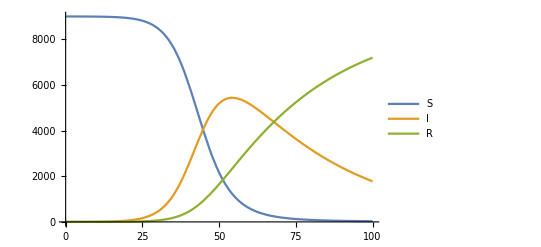

```mathematica
sols = {Total[s[t]],Total[i[t]],Total[r[t]]}/.sol//Flatten;
Plot[sols, {t,t1,t2},
PlotLegends->{"S", "I", "R"}]
```